```mathematica
Manipulate[
ss=FindRoot[muu==ddd*Exp[-(4 Pi)/muu],{muu,10,2,100}];
Show[Plot[{mu,ddd*Exp[-(4 Pi)/mu]},{mu,0,100}],
Graphics[{PointSize[Large],Point[{muu,muu}/.ss]}]],{ddd,35,200}]
```

```mathematica
Manipulate[
ss=FindRoot[muu==ddd*Exp[-(4 Pi)/muu],{muu,10,2,100}];
Show[Plot[{mu,ddd*Exp[-(4 Pi)/mu]},{mu,0,100}],
Graphics[{PointSize[Large],Point[{muu,muu}/.ss]}]],{ddd,35,200}]
```

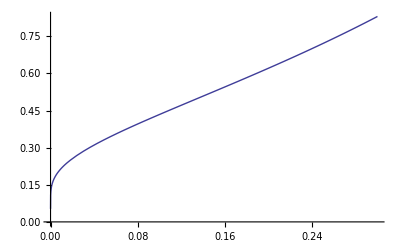

```mathematica
Plot[-1/Log[x],{x,0,0.3}]
```

```mathematica
reso=1/100000
liveembe=Join[{{0,0}},Table[{x,y/.FindRoot[(4 Pi)/y==-Log[2 x]-Log[y],{y,1,1/200,4 Pi}]},{x, reso,1/(8 Pi Exp[1])-1reso,reso}]];
correctus=Join[{{0,0}},Table[{x,y/.FindRoot[(4 Pi)/y==-Log[2 x]-Log[y]-(4 Pi)/(y^2(Log[2 x y])^2),{y,1,1/200,4 Pi}]},{x, reso,1/(8 Pi Exp[1])-80reso,reso}]];
```

1/100000

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

FindRoot::reged: The point {12.566370614359172`} is at the edge of the search region {0.005`, 12.566370614359172`} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot will be suppressed during this calculation.

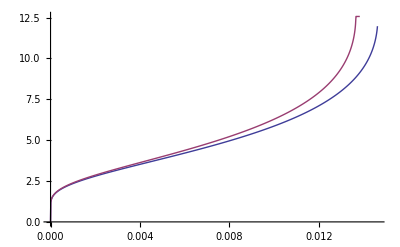

```mathematica
ListPlot[{liveembe,correctus}, AxesOrigin->{0,0},Joined->True]
```

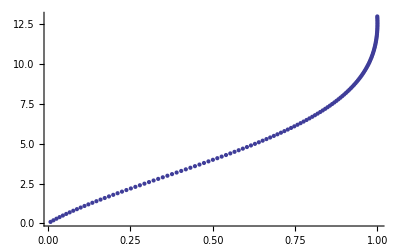

```mathematica
ListPlot[Table[{y/(4 Pi - y Log[(4 Pi)/y]),y},{y,0.1, 13,0.1}]]
```